```mathematica
齿轮
```

```mathematica
extrude[p_Polygon,z_]:=Module[{pts=p[[1]]},Polygon/@{Append[#,0]&/@pts,Append[#,z]&/@pts,Join[Append[#,0]&/@#,Append[#,z]&/@Reverse[#]]&/@Partition[List@@pts,2,1,1]}]
pentagon=Polygon[Array[{Cos[2 π #/5],Sin[2 π #/5]}&,5]];
Graphics3D[{Gray,extrude[pentagon,2]},Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
Graphics3D[{EdgeForm[],Polygon[{{0,0,4},{0,1,4},{0,0,5}}],Polygon[{{0,0,4},{1,0,4},{1,0,5},{0,0,5}}],Polygon[{{0,0,5},{1,0,5},{1,1,4},{0,1,4}}],Polygon[{{1,0,4},{1,1,4},{1,0,5}}],Cuboid[{0,0,1},{1,1,4}],Cuboid[{0,0,0},{1,6,1}],Cuboid[{0,5,0},{-5,6,1}]},Boxed->False,Axes->None,AspectRatio->Automatic,PlotRange->{{-6,6},{0,6},{-1,5}},ViewPoint->{50,-50.3, 50}]
```

-Graphics3D-

```mathematica
Manipulate[
r={x,y};p=Polygon[{{0,0},{0,a},{(√3)/2 c,a-c/2},{(√3)/2 c,c/2+d},{(√3)/2 b,b/2+d},{(√3)/2 b,b/2}}];Graphics[{Pink,p,Yellow,Rotate[p,(2π)/3,r],Orange,Rotate[p,(4π)/3,r]}],{{a,5},1,10},{{b,6},1,10},{{c,1},1,10},{{d,1},1,10},{{x,0},-5,5},{{y,0},-5,5}]
```

```mathematica
SolveValues[(1+θ)Cos[θ]==-1,θ]
```

SolveValues::nsmet: This system cannot be solved with the methods available to SolveValues.

SolveValues[{(1+θ) Cos[θ]==-1},θ]

```mathematica
DynamicModule[{c1,c2,c3},
Manipulate[c1=Circle[{0,0},{a,b}];c2=Circle[{k a-a,0},{a,b}k,{π,2π}];c3=Circle[{0,0},{a,b}(2k-1)];Graphics[{Thick,c1,c2,Rotate[c2,π,{0,0}],c3}],{{a,2},1,5},{{b,1},1,5},{{k,2},1,5}]
]
```

```mathematica
DynamicModule[{c1,c2,c3},
Manipulate[c1=Circle[{0,0},{a,b}];c2=Circle[{(k a-a)/2,0},{ a,b}(k+1)/2,{π,2π}];c3=Circle[{0,0},{a,b}k];Graphics[{Thick,c1,c2,Rotate[c2,π,{0,0}],c3}],{{a,2},1,5},{{b,1},1,5},{{k,2},1,5}]
]
```

### 利用复数绘制

```mathematica
Manipulate[ParametricPlot[{1,0}(Floor[θ,π]a-a)+{a Cos[θ],b Sin[θ]}(Floor[θ,π]+1),{θ,0,5π}],{{a,2},1,5},{{b,1},1,5}]
```

Show::gcomb: 无法合并 Show[,] 中的图形对象.

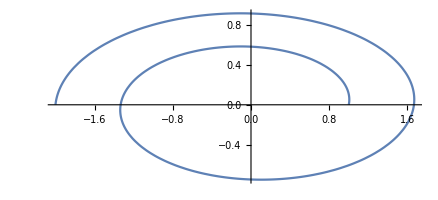
Show[-Graphics-,-Graphics-]

```mathematica
Show[pp,GeometricTransformation[pp,π]]
```

```mathematica
?Torus
```

```mathematica
KnotData["Trefoil"]
```